{c→15.5773,k→0.270406,b→19.5171}

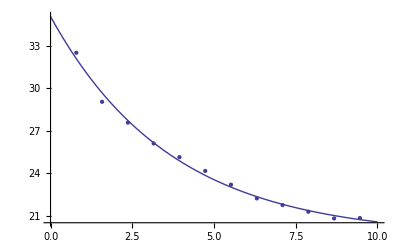

```mathematica
data = {{0.7886,32.5278260674},
{1.5772,29.0556521349},
{2.3658 ,27.5834782023},
{3.1544,26.1113042698},
{3.943,25.1391303372},
{4.7316,24.1669564046},
{5.5202,23.1947824721},
{6.3088,22.2226085395},
{7.0974,21.750434607},
{7.886,21.2782606744},
{8.6746,20.8060867418},
{9.4632,20.8339128093}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```